```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = "../shown results";
SetDirectory[workingDirectory];
file= OpenRead["../logs/log_search.txt"];
workingDirectory = CreateDirectory["search"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

mapSearchResults = filelist[[3;;;;4]];
binarySearchResults = filelist[[2;;;;4]];
linearSearchResults = filelist[[1;;;;4]];
linearSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,linearSearchResults];
binarySearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,binarySearchResults];
mapSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,mapSearchResults];
linearSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,linearSearchResults];
binarySearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,binarySearchResults];
mapSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,mapSearchResults];
Plot1 = Show[ListLogPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key (rs, simple, default) (Log scale)", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListLogPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}]];
```

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\search\\" already exists.

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = "../shown results";
SetDirectory[workingDirectory];
file= OpenRead["../logs/log_hash.txt"];
workingDirectory = CreateDirectory["hash"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

defaultSearchResults = filelist[[3;;;;4]];
rsSearchResults = filelist[[2;;;;4]];
simpleSearchResults = filelist[[1;;;;4]];
simpleSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,simpleSearchResults];
rsSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,rsSearchResults];
defaultSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,defaultSearchResults];
simpleSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,simpleSearchResults];
rsSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,rsSearchResults];
defaultSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,defaultSearchResults];
Plot2= Show[ListLogPlot[simpleSearchResults,Joined->True,PlotStyle->Yellow,PlotLegends->{"Simple hash (search)"}, AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListLogPlot[rsSearchResults,Joined->True,PlotStyle->Black,PlotLegends->{"RS hash (search)"}],
ListLogPlot[defaultSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Default hash (search)"}]];
```

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\hash\\" already exists.

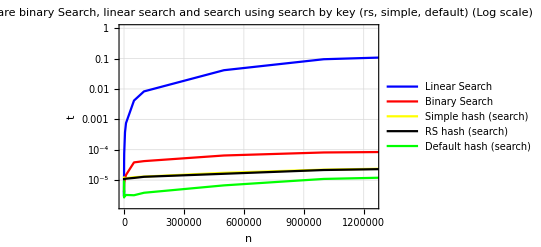

```mathematica
Plot3 = Show[Plot1, Plot2]
```

```mathematica
Export["../search_compare_all.gif",Plot3,ImageSize->2048];
```